# SSI diploids

## Codominant or recessive

```mathematica
ClearAll["Global`*"]
```

Fitness and selfing rates :

```mathematica
Wbar = 1 - δ (x1+x3);
W1 = 1- δ;
W2 = 1;
W3 = 1-δ;
W4 = 1;
a1= (s W1)/(s W1 + (1-s)*Wbar);
a2 =(s W2)/(s W2 + (1-s)*Wbar);
a3 = 0;
a4 = 0;
```

Defining the quantities necessary for the recursion equations :

```mathematica
x0 = 1-x1-x2-x3-x4;
qCC= (W1 x1+W2 x2)/(Wbar);
qCi= (W3 x3 + W4 x4)(n-1)/(Wbar n);
qCij =(n-2)(W3 x3 + W4 x4)/(Wbar n);
qii = x0 (n-2)/(Wbar n);
qijij = x0(n-2) (n-3)/(Wbar n (n-1));
q = qCC + 1/(2 Wbar)(W3 x3 + W4 x4);
```

Recursion equations :

```mathematica
x1p = W1 a1 x1 + W2 a2 x2;
x2p = W1 (1-a1) x1 q + W2 (1-a2) x2 q + 1/2(W3(1-a3) x3 + W4 (1-a4) x4)(qCC+1/2 qCi)/(qCC + qCi + qii);
x3p = 0;
x4p = W1(1-a1) x1(1-q) + W2 (1-a2) x2(1-q)+ 1/2(W3 (1-a3)x3 + W4(1-a4)x4) + x0*(qCC + 1/2 qCij)/(qCC+qCij+qijij);
```

```mathematica
recur=Simplify[{x1p/Wbar,x2p/Wbar,x3p/Wbar,x4p/Wbar}]
```

{((s x2)/(1+(-1+s) x1 δ+(-1+s) x3 δ)+(s x1 (-1+δ)^2)/(1-x1 δ-x3 δ+s (-1+x1+x3) δ))/(1-(x1+x3) δ),-(((-1+s) x2 (2 x2+x3+x4-2 x1 (-1+δ)-x3 δ))/(2 (1+(-1+s) x1 δ+(-1+s) x3 δ))+((-1+s) x1 (-1+δ) (-2 x2-x3-x4+2 x1 (-1+δ)+x3 δ))/(2-2 x1 δ-2 x3 δ+2 s (-1+x1+x3) δ)+((x3+x4-x3 δ) (-x4+x3 (-1+δ)+n (2 x2+x3+x4-2 x1 (-1+δ)-x3 δ)))/(-4 (-2+2 x1+2 x2+x3+x4+x3 δ)+4 n (-1+x1 δ+x3 δ)))/(1-(x1+x3) δ),0,1/(2 (1-(x1+x3) δ))(x3+x4-x3 δ+((-1+s) x2 (-2+2 x1+2 x2+x3+x4+x3 δ))/(1+(-1+s) x1 δ+(-1+s) x3 δ)-((-1+s) x1 (-1+δ) (-2+2 x1+2 x2+x3+x4+x3 δ))/(1-x1 δ-x3 δ+s (-1+x1+x3) δ)-((-1+n) (-1+x1+x2+x3+x4) (2 (x3+x4-x3 δ)-n (2 x2+x3+x4-2 x1 (-1+δ)-x3 δ)))/(-6+6 x1+6 x2+4 x3+4 x4+2 x3 δ+n^2 (-1+x1 δ+x3 δ)-n (-5+4 x2+2 x3+2 x4+3 x3 δ+x1 (4+δ))))}

```mathematica
recur2=Simplify[Normal[Series[recur/.x1->x1 eps/.x2->x2 eps/.x3->x3 eps/.x4->x4 eps,{eps,0,1}]]/.eps->1]
```

{s (x2+(x1 (-1+δ)^2)/(1-s δ)),0,0,1/2 (-2 (-1+s) x2+x3+x4-x3 δ-(2 (-1+s) x1 (-1+δ))/(-1+s δ)-((-1+n) (2 (x3+x4-x3 δ)-n (2 x2+x3+x4-2 x1 (-1+δ)-x3 δ)))/(6-5 n+n^2))}

```mathematica
recur3=FullSimplify[{recur2⟦1⟧,recur2⟦4⟧}/.x3->0/.x2->0]
```

{(s x1 (-1+δ)^2)/(1-s δ),1/2 (x4+((-1+n) (-2 x4+n (x4-2 x1 (-1+δ))))/(6-5 n+n^2)-(2 (-1+s) x1 (-1+δ))/(-1+s δ))}

```mathematica
mat=FullSimplify[{{Coefficient[recur3⟦1⟧,x1],Coefficient[recur3⟦1⟧,x4]},{Coefficient[recur3⟦2⟧,x1],Coefficient[recur3⟦2⟧,x4]}}]
```

{{(s (-1+δ)^2)/(1-s δ),0},{-((-1+δ) (6 (-1+s)+n (6-s (5+δ)+n (-2+s+s δ))))/((-3+n) (-2+n) (-1+s δ)),1+1/(-3+n)}}

### Routh - Hurwitz stability conditions

```mathematica
Q = CharacteristicPolynomial[mat,λ]
```

s/(1-s δ)+s/((-3+n) (1-s δ))-(2 s δ)/(1-s δ)-(2 s δ)/((-3+n) (1-s δ))+(s δ^2)/(1-s δ)+(s δ^2)/((-3+n) (1-s δ))-λ-λ/(-3+n)-(s λ)/(1-s δ)+(2 s δ λ)/(1-s δ)-(s δ^2 λ)/(1-s δ)+λ^2

```mathematica
Qr = Q/.λ->1+r
```

-1-r-(1+r)/(-3+n)+(1+r)^2+s/(1-s δ)+s/((-3+n) (1-s δ))-((1+r) s)/(1-s δ)-(2 s δ)/(1-s δ)-(2 s δ)/((-3+n) (1-s δ))+(2 (1+r) s δ)/(1-s δ)+(s δ^2)/(1-s δ)+(s δ^2)/((-3+n) (1-s δ))-((1+r) s δ^2)/(1-s δ)

```mathematica
q0 = Coefficient[Qr, r, 2]
```

1

```mathematica
q1=FullSimplify[Coefficient[Qr,r,1]]
```

(4+s (-3+(2-3 δ) δ)+n (-1+s+s (-1+δ) δ))/((-3+n) (-1+s δ))

```mathematica
q2 = FullSimplify[Coefficient[Qr,r,0]]
```

(1+s (-1+δ-δ^2))/((-3+n) (-1+s δ))

```mathematica
Plot3D[q1/.n->20,{s,0,1},{δ,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[q2/.n->100,{s,0,1},{δ,0,1}]
```

-Graphics3D-

```mathematica
polyq2 = FullSimplify[Numerator[Together[q2]]]
```

1+s (-1+δ-δ^2)

```mathematica
Reduce[Denominator[Together[q2]]<0 &&0<=δ<=1 &&0<s<1&&n>5,δ, Reals]
```

0<s<1&&n>5&&0≤δ≤1

```mathematica
Reduce[polyq2<0 &&0<=δ<=1 &&0<s<1&&n>5,δ, Reals]
```

False

## Dominant (without W_h, i.e. neglecting selfed SiSi individuals)

Fitness and selfing rates :

```mathematica
Wbar = 1 - δ (x1+x3);
W1 = 1- δ;
W2 = 1;
W3 = 1-δ;
W4 = 1;
b1= (s W1)/(s W1 + (1-s)*Wbar);
b2 =(s W2)/(s W2 + (1-s)*Wbar);
b3 = (s W3)/ (s W3 +(1-s)*Wbar);
b4 = (s W4)/(s W4 + (1-s)*Wbar);
```

Some quantities :

```mathematica
x0 = 1-x1-x2-x3-x4;
qCC= (W1 x1+W2 x2)/(Wbar);
qCI = 1/Wbar(W3 x3 + W4 x4);
qCi= (W3 x3 + W4 x4)(n-1)/(Wbar n);
qCij =(n-2)(W3 x3 + W4 x4)/(Wbar n);
qii = x0 (n-1)(n-1)/(Wbar n*n);
qijij = x0(n-2) (n-2)/(Wbar n n);
q = qCC + 1/(2 Wbar)(W3 x3 + W4 x4);
```

Recursion equations (dominant case) :

```mathematica
x1pD = W1 b1 x1 + W2 b2 x2 + 1/4 W3 b3 x3 + 1/4 W4 b4 x4;
x2pD = W1 (1-b1) x1 q + W2 (1-b2) x2 q + 1/2(W3(1-b3) x3 + W4 (1-b4) x4)q/(qCC + qCI + qii);
x3pD = 1/2 W3 b3 x3 + 1/2 W4 b4 x4;
x4pD = W1(1-b1) x1(1-q) + W2 (1-b2) x2(1-q)+ 1/2(W3 (1-b3)x3 + W4(1-b4)x4) + x0*q/(qCC + qCI + qijij);
```

```mathematica
recurD=Simplify[{x1pD/Wbar,x2pD/Wbar,x3pD/Wbar,x4pD/Wbar}]
```

{(s ((4 x2)/(1+(-1+s) x1 δ+(-1+s) x3 δ)+x4/(1+(-1+s) x1 δ+(-1+s) x3 δ)+((4 x1+x3) (-1+δ)^2)/(1-x1 δ-x3 δ+s (-1+x1+x3) δ)))/(4 (1-(x1+x3) δ)),1/(4 (-1+x1 δ+x3 δ)^2)(2 x2+x3+x4-2 x1 (-1+δ)-x3 δ) (-(2 (-1+s) x1 (-1+δ) (-1+x1 δ+x3 δ))/(1-x1 δ-x3 δ+s (-1+x1+x3) δ)+2 x2 (1-s/(1+(-1+s) x1 δ+(-1+s) x3 δ))-(n^2 (-1+s) (-1+x1 δ+x3 δ)^2 ((-1+s) x3^2 (-1+δ) δ+x3 (-1+(1+x1-s x1+x4-s x4) δ+(-1+s) x1 δ^2)+x4 (-1+x1 δ+s (δ-x1 δ))))/((1+(-1+s) x1 δ+(-1+s) x3 δ) (1-x1 δ-x3 δ+s (-1+x1+x3) δ) (-1+x1+x2+x3+x4-2 n (-1+x1+x2+x3+x4)+n^2 (-1+x1 δ+x3 δ)))),(s (x4/(1+(-1+s) x1 δ+(-1+s) x3 δ)+(x3 (-1+δ)^2)/(1-x1 δ-x3 δ+s (-1+x1+x3) δ)))/(2 (1-(x1+x3) δ)),-1/(2 (1-(x1+x3) δ))(-x4+(s x4)/(1+(-1+s) x1 δ+(-1+s) x3 δ)-((-1+s) x2 (-2+2 x1+2 x2+x3+x4+x3 δ))/(1+(-1+s) x1 δ+(-1+s) x3 δ)+((-1+s) x1 (-1+δ) (-2+2 x1+2 x2+x3+x4+x3 δ))/(1-x1 δ-x3 δ+s (-1+x1+x3) δ)+((-1+s) x3 (-1+δ) (-1+x1 δ+x3 δ))/(1-x1 δ-x3 δ+s (-1+x1+x3) δ)+(n^2 (-1+x1+x2+x3+x4) (-2 x2-x3-x4+2 x1 (-1+δ)+x3 δ))/(4 (-1+x1+x2+x3+x4)-4 n (-1+x1+x2+x3+x4)+n^2 (-1+x1 δ+x3 δ)))}

First order simplification :

```mathematica
recurD2=Simplify[Normal[Series[recurD/.x1->x1 eps/.x2->x2 eps/.x3->x3 eps/.x4->x4 eps,{eps,0,1}]]/.eps->1]
```

{1/4 s (4 x2+x4+((4 x1+x3) (-1+δ)^2)/(1-s δ)),0,1/2 s (x4+(x3 (-1+δ)^2)/(1-s δ)),1/2 (-2 (-1+s) x2+x4-s x4-(2 (-1+s) x1 (-1+δ))/(-1+s δ)-((-1+s) x3 (-1+δ))/(-1+s δ)+(n^2 (2 x2+x3+x4-2 x1 (-1+δ)-x3 δ))/(-2+n)^2)}

```mathematica
recurD3=FullSimplify[{recurD2⟦1⟧,recurD2⟦3⟧,recurD2⟦4⟧}/. x2-> 0]
```

{1/4 s (x4+((4 x1+x3) (-1+δ)^2)/(1-s δ)),1/2 s (x4+(x3 (-1+δ)^2)/(1-s δ)),1/2 ((n^2 (2 x1+x3+x4-(2 x1+x3) δ))/(-2+n)^2+((-1+s) (2 x1+x3+x4-(2 x1+x3+s x4) δ))/(-1+s δ))}

```mathematica
matD=FullSimplify[{{Coefficient[recurD3⟦1⟧,x1],Coefficient[recurD3⟦1⟧,x3],Coefficient[recurD3⟦1⟧,x4]},{Coefficient[recurD3⟦2⟧,x1],Coefficient[recurD3⟦2⟧,x3],Coefficient[recurD3⟦2⟧,x4]}, {Coefficient[recurD3⟦3⟧,x1],Coefficient[recurD3⟦3⟧,x3],Coefficient[recurD3⟦3⟧,x4]}}]
```

{{-(s (-1+δ)^2)/(-1+s δ),-(s (-1+δ)^2)/(-4+4 s δ),s/4},{0,-(s (-1+δ)^2)/(-2+2 s δ),s/2},{-((-1+δ) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/((-2+n)^2 (-1+s δ)),-((-1+δ) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/(2 (-2+n)^2 (-1+s δ)),(2+(-2+n) n)/(-2+n)^2-s/2}}

#### Routh - Hurwitz conditions for stability

On calcule le polynôme caractéristique de la matrice matD :

```mathematica
P = CharacteristicPolynomial[matD, λ]
```

-1/2 s (-(s (-1+δ)^3 (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/((-2+n)^2 (-1+s δ) (-4+4 s δ))-((-1+δ) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))) (-(s (-1+δ)^2)/(-1+s δ)-λ))/(2 (-2+n)^2 (-1+s δ)))+((s (-1+δ) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/(4 (-2+n)^2 (-1+s δ))+((2+(-2+n) n)/(-2+n)^2-s/2-λ) (-(s (-1+δ)^2)/(-1+s δ)-λ)) (-(s (-1+δ)^2)/(-2+2 s δ)-λ)

On subsitute 1 + r à λ pour obtenir ensuite les conditions RH en discret :

```mathematica
Pr = -P/.λ->1+r
```

-((-1-r-(s (-1+δ)^2)/(-2+2 s δ)) ((-1+(2+(-2+n) n)/(-2+n)^2-r-s/2) (-1-r-(s (-1+δ)^2)/(-1+s δ))+(s (-1+δ) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/(4 (-2+n)^2 (-1+s δ))))+1/2 s (-(s (-1+δ)^3 (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/((-2+n)^2 (-1+s δ) (-4+4 s δ))-((-1+δ) (-1-r-(s (-1+δ)^2)/(-1+s δ)) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/(2 (-2+n)^2 (-1+s δ)))

On calcule les coefficients de ce polynômes en r, en s' assurant que le coefficient dominant est 1 :

```mathematica
c0 = Coefficient[Pr, r, 3]
```

1

```mathematica
c1 = FullSimplify[Coefficient[Pr, r^2]/c0];
c2 = FullSimplify[Coefficient[Pr,r]/c0];
c3 = FullSimplify[Coefficient[Pr, r,0]/c0];
```

Les conditions RH sont : c1 > 0, c3 > 0 et c1c2 - c3 > 0. Si ces conditions sont respectées, alors l' équilibre est stable .
  On vérifier d' abord les deux premières conditions :

```mathematica
Plot3D[c3/.n ->10,{s,0,1},{δ,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[c1/.n->5,{s,0,1},{δ,0,1}]
```

-Graphics3D-

```mathematica
f=Function[{s,δ},Evaluate[(c1 c2-c3)/. n->10]];
Plot3D[f[α,δ],{α,0,1},{δ,0,1}]
```

-Graphics3D-

```mathematica
polyDelta = FullSimplify[Numerator[Together[c3]]]
```

(-2+s+s δ^2) (4 (-1+s)+n^2 s (-1+2 δ) (-1+s δ)+4 s δ (-2+δ+s δ)-4 n (-1+s-2 s δ+s (1+s) δ^2))

```mathematica
Reduce[Denominator[Together[c3]]>0  &&0<=δ<=1 &&0<s<1&&n>5, Reals]
```

0≤δ≤1&&n>5&&0<s<1

```mathematica
Reduce[polyDelta>0  &&0<=δ<=1 &&0<s<1&&n>5,δ, Reals]
```

n>2 (2+√2)&&(-4+4 n)/(4-4 n+n^2)<s<1&&(8-8 n+2 n^2+n^2 s)/(4 (2-2 n+2 s-2 n s+n^2 s))-1/4 √((64-128 n+64 n^2+64 s-128 n s+112 n^2 s-48 n^3 s+4 n^4 s-64 s^2+128 n s^2-96 n^2 s^2+32 n^3 s^2-4 n^4 s^2+n^4 s^3)/(s (2-2 n+2 s-2 n s+n^2 s)^2))<δ≤1

c3 peut être négatif, et l’équilibre est stable lorsque c3>0. On cherche donc la limite c3=0 pour déterminer la dépression de consanguinité limite qui fait basculer le système d’une situation où il y invasion des allèles SC:

```mathematica
d4 = FullSimplify[Coefficient[polyDelta,δ^4]]
```

2 s^2 (2 (1+s)+n (-2+(-2+n) s))

```mathematica
d3 = FullSimplify[Coefficient[polyDelta,δ^3]]
```

-s^2 (8+n (-8+n (2+s)))

```mathematica
d2 = FullSimplify[Coefficient[polyDelta,δ^2]]
```

s (12 (-1+n)-3 n^2 s+2 (2+(-2+n) n) s^2)

```mathematica
d1 = FullSimplify[Coefficient[polyDelta,δ^1]]
```

-((-2+s) s (8+n (-8+n (2+s))))

```mathematica
d0 = FullSimplify[(polyDelta /.δ->0)]
```

(-2+s) (4 (-1+n)+(-2+n)^2 s)

La dépression de consanguinité δ limite est solution de l’équation d4 δ^4+d3 δ^3+d2 δ^2+d1 δ+d0=0, avec

```mathematica
d4 = 2 s^2 (2 (1+s)+n (-2+(-2+n) s));
d3 = -s^2 (8+n (-8+n (2+s)));
d2 = s (12 (-1+n)-3 n^2 s+2 (2+(-2+n) n) s^2);
d1 = -((-2+s) s (8+n (-8+n (2+s))));
d0 =(-2+s) (4 (-1+n)+(-2+n)^2 s);
```

```mathematica
cond= d4 δ^4+d3 δ^3+d2 δ^2+d1 δ+d0
```

(-2+s) (4 (-1+n)+(-2+n)^2 s)-(-2+s) s (8+n (-8+n (2+s))) δ+s (12 (-1+n)-3 n^2 s+2 (2+(-2+n) n) s^2) δ^2-s^2 (8+n (-8+n (2+s))) δ^3+2 s^2 (2 (1+s)+n (-2+(-2+n) s)) δ^4

On trace le δ limite en fonction du taux d’autofécondation s, pour un n donné:

```mathematica
n = 19;
```

```mathematica
nbpts=100;s=.;
tt=Table[{N[i/nbpts],0},{i,0,nbpts}];
Do[{s=tt⟦i+1,1⟧;tt⟦i+1,2⟧=δ/.FindRoot[polyDelta==0,{δ,0.7}]},{i,0,nbpts}]
```

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {δ} = {0.7}.

ReplaceAll::reps: {FindRoot[polyDelta==0,{δ,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {δ} = {0.7}.

ReplaceAll::reps: {FindRoot[polyDelta==0,{δ,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {δ} = {0.7}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[polyDelta==0,{δ,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

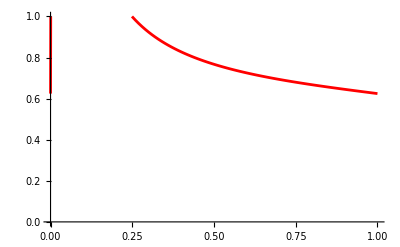

```mathematica
ListPlot[tt,Joined->True,PlotStyle->Hue[0],PlotRange->{{0,1},{0,1}}]
```

```mathematica
tt
```

{{0.,0.624567},{0.01,7.13812},{0.02,4.55428},{0.03,3.48427},{0.04,2.88143},{0.05,2.48991},{0.06,2.21345},{0.07,2.00709},{0.08,1.8468},{0.09,1.71851},{0.1,1.61338},{0.11,1.52561},{0.12,1.45116},{0.13,1.3872},{0.14,1.33162},{0.15,1.28287},{0.16,1.23975},{0.17,1.20133},{0.18,1.16686},{0.19,1.13578},{0.2,1.10758},{0.21,1.0819},{0.22,1.05839},{0.23,1.03679},{0.24,1.01688},{0.25,0.998461},{0.26,0.981368},{0.27,0.965462},{0.28,0.950621},{0.29,0.936739},{0.3,0.923724},{0.31,0.911495},{0.32,0.899982},{0.33,0.889122},{0.34,0.878858},{0.35,0.869142},{0.36,0.859929},{0.37,0.85118},{0.38,0.842858},{0.39,0.834933},{0.4,0.827374},{0.41,0.820156},{0.42,0.813254},{0.43,0.806647},{0.44,0.800315},{0.45,0.79424},{0.46,0.788406},{0.47,0.782796},{0.48,0.777398},{0.49,0.772197},{0.5,0.767183},{0.51,0.762343},{0.52,0.757668},{0.53,0.753149},{0.54,0.748776},{0.55,0.744542},{0.56,0.740438},{0.57,0.736457},{0.58,0.732593},{0.59,0.72884},{0.6,0.725191},{0.61,0.721642},{0.62,0.718186},{0.63,0.714819},{0.64,0.711537},{0.65,0.708335},{0.66,0.705209},{0.67,0.702156},{0.68,0.699171},{0.69,0.69625},{0.7,0.693392},{0.71,0.690592},{0.72,0.687847},{0.73,0.685156},{0.74,0.682514},{0.75,0.67992},{0.76,0.67737},{0.77,0.674863},{0.78,0.672397},{0.79,0.669968},{0.8,0.667575},{0.81,0.665216},{0.82,0.662889},{0.83,0.660592},{0.84,0.658324},{0.85,0.656081},{0.86,0.653864},{0.87,0.65167},{0.88,0.649497},{0.89,0.647343},{0.9,0.645209},{0.91,0.643091},{0.92,0.640989},{0.93,0.638901},{0.94,0.636825},{0.95,0.634761},{0.96,0.632707},{0.97,0.630662},{0.98,0.628625},{0.99,0.626593},{1.,0.624567}}

## Dominant (with Wh, i.e. taking selfed SiSi individuals into account)

```mathematica
ClearAll["Global`*"]
```

```mathematica
Wbar = 1 - δ (x1+x3+xh);
W1 = 1- δ;
W2 = 1;
W3 = 1-δ;
W4 = 1;
Wh = 1 - δ;
b1= (s W1)/(s W1 + (1-s)*Wbar);
b2 =(s W2)/(s W2 + (1-s)*Wbar);
b3 = (s W3)/ (s W3 +(1-s)*Wbar);
b4 = (s W4)/(s W4 + (1-s)*Wbar);
```

Some frequencies

```mathematica
x0 = 1-x1-x2-x3-x4;
xh = 1/2 x3;
qCC= (W1 x1+W2 x2)/(Wbar);
qCI = 1/Wbar(W3 x3 + W4 x4);
qCi= (W3 x3 + W4 x4)(n-1)/(Wbar n);
qCij =(n-2)(W3 x3 + W4 x4)/(Wbar n);
pii = ((x0-Wh xh) (n-1)(n-1)/(Wbar n*n)) + (Wh xh (n-1)/(Wbar n n));
pijij = ((x0-Wh xh) (n-2)(n-2)/(Wbar n*n)) + (Wh xh (n-2)/(Wbar n n));
q = qCC + 1/(2 Wbar)(W3 x3 + W4 x4);
```

Recursion equations

```mathematica
x1pD = W1 b1 x1 + W2 b2 x2 + 1/4 W3 b3 x3 + 1/4 W4 b4 x4;
x2pD = W1 (1-b1) x1 q + W2 (1-b2) x2 q + 1/2(W3(1-b3) x3 + W4 (1-b4) x4)q/(qCC + qCI + pii);
x3pD = 1/2 W3 b3 x3 + 1/2 W4 b4 x4;
x4pD = W1(1-b1) x1(1-q) + W2 (1-b2) x2(1-q)+ 1/2(W3 (1-b3)x3 + W4(1-b4)x4) + (x0-Wh xh)*q/(qCC + qCI + pijij)+ Wh xh q/(qCC + qCI +pii);
```

```mathematica
recurD=Simplify[{x1pD/Wbar,x2pD/Wbar,x3pD/Wbar,x4pD/Wbar}]
```

{(s ((8 x2)/(2+2 (-1+s) x1 δ+3 (-1+s) x3 δ)+(2 x4)/(2+2 (-1+s) x1 δ+3 (-1+s) x3 δ)+(8 x1 (-1+δ)^2)/(2-2 x1 δ-3 x3 δ+s (-2+2 x1+3 x3) δ)+(2 x3 (-1+δ)^2)/(2-2 x1 δ-3 x3 δ+s (-2+2 x1+3 x3) δ)))/(4 (1-(x1+(3 x3)/2) δ)),1/(-2+2 x1 δ+3 x3 δ)^2(2 x2+x3+x4-2 x1 (-1+δ)-x3 δ) (-(2 (-1+s) x1 (-1+δ) (-2+2 x1 δ+3 x3 δ))/(2-2 x1 δ-3 x3 δ+s (-2+2 x1+3 x3) δ)+2 x2 (1-(2 s)/(2+2 (-1+s) x1 δ+3 (-1+s) x3 δ))-(n^2 (-1+s) (-2+2 x1 δ+3 x3 δ)^2 (3 (-1+s) x3^2 (-1+δ) δ+x3 (-2+(2+2 x1-2 s x1+3 x4-3 s x4) δ+2 (-1+s) x1 δ^2)+2 x4 (-1+x1 δ+s (δ-x1 δ))))/((2+2 (-1+s) x1 δ+3 (-1+s) x3 δ) (2-2 x1 δ-3 x3 δ+s (-2+2 x1+3 x3) δ) (-n (-4+4 x1+4 x2+7 x3+4 x4-3 x3 δ)+2 (-1+x1+x2+2 x3+x4-x3 δ)+n^2 (-2+x3+2 x1 δ+x3 δ)))),(s ((2 x4)/(2+2 (-1+s) x1 δ+3 (-1+s) x3 δ)+(2 x3 (-1+δ)^2)/(2-2 x1 δ-3 x3 δ+s (-2+2 x1+3 x3) δ)))/(2 (1-(x1+(3 x3)/2) δ)),-1/(2 (1-(x1+(3 x3)/2) δ))(-x4+(2 s x4)/(2+2 (-1+s) x1 δ+3 (-1+s) x3 δ)-(2 (-1+s) x2 (-2+2 x1+2 x2+x3+x4+2 x3 δ))/(2+2 (-1+s) x1 δ+3 (-1+s) x3 δ)+(2 (-1+s) x1 (-1+δ) (-2+2 x1+2 x2+x3+x4+2 x3 δ))/(2-2 x1 δ-3 x3 δ+s (-2+2 x1+3 x3) δ)+((-1+s) x3 (-1+δ) (-2+2 x1 δ+3 x3 δ))/(2-2 x1 δ-3 x3 δ+s (-2+2 x1+3 x3) δ)+(n^2 (-2+2 x1+2 x2+3 x3+2 x4-x3 δ) (-2 x2-x3-x4+2 x1 (-1+δ)+x3 δ))/(-8+8 x1+8 x2+14 x3+8 x4-6 x3 δ-n (-8+8 x1+8 x2+13 x3+8 x4-5 x3 δ)+n^2 (-2+x3+2 x1 δ+x3 δ))+(n^2 x3 (-1+δ) (-2 x2-x3-x4+2 x1 (-1+δ)+x3 δ))/(-n (-4+4 x1+4 x2+7 x3+4 x4-3 x3 δ)+2 (-1+x1+x2+2 x3+x4-x3 δ)+n^2 (-2+x3+2 x1 δ+x3 δ)))}

```mathematica
recurD2=Simplify[Normal[Series[recurD/.x1->x1 eps/.x2->x2 eps/.x3->x3 eps/.x4->x4 eps,{eps,0,1}]]/.eps->1]
```

{1/4 s (4 x2+x4-(4 x1 (-1+δ)^2)/(-1+s δ)-(x3 (-1+δ)^2)/(-1+s δ)),0,1/2 s (x4-(x3 (-1+δ)^2)/(-1+s δ)),1/2 (-2 (-1+s) x2+x4-s x4-(2 (-1+s) x1 (-1+δ))/(-1+s δ)-((-1+s) x3 (-1+δ))/(-1+s δ)+(n^2 (2 x2+x3+x4-2 x1 (-1+δ)-x3 δ))/(-2+n)^2)}

```mathematica
recurD3=FullSimplify[{recurD2⟦1⟧,recurD2⟦3⟧,recurD2⟦4⟧}/. x2-> 0]
```

{(s (-4 x1 (-1+δ)^2-x3 (-1+δ)^2+x4 (-1+s δ)))/(-4+4 s δ),1/2 s (x4-(x3 (-1+δ)^2)/(-1+s δ)),1/2 ((n^2 (2 x1+x3+x4-(2 x1+x3) δ))/(-2+n)^2+((-1+s) (2 x1+x3+x4-(2 x1+x3+s x4) δ))/(-1+s δ))}

```mathematica
matD=FullSimplify[{{Coefficient[recurD3⟦1⟧,x1],Coefficient[recurD3⟦1⟧,x3],Coefficient[recurD3⟦1⟧,x4]},{Coefficient[recurD3⟦2⟧,x1],Coefficient[recurD3⟦2⟧,x3],Coefficient[recurD3⟦2⟧,x4]}, {Coefficient[recurD3⟦3⟧,x1],Coefficient[recurD3⟦3⟧,x3],Coefficient[recurD3⟦3⟧,x4]}}]
```

{{-(s (-1+δ)^2)/(-1+s δ),-(s (-1+δ)^2)/(-4+4 s δ),s/4},{0,-(s (-1+δ)^2)/(-2+2 s δ),s/2},{-((-1+δ) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/((-2+n)^2 (-1+s δ)),-((-1+δ) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/(2 (-2+n)^2 (-1+s δ)),(2+(-2+n) n)/(-2+n)^2-s/2}}

### Routh-Hurwitz stability conditions

```mathematica
P = CharacteristicPolynomial[matD, λ]
```

-1/2 s (-(s (-1+δ)^3 (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/((-2+n)^2 (-1+s δ) (-4+4 s δ))-((-1+δ) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))) (-(s (-1+δ)^2)/(-1+s δ)-λ))/(2 (-2+n)^2 (-1+s δ)))+((s (-1+δ) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/(4 (-2+n)^2 (-1+s δ))+((2+(-2+n) n)/(-2+n)^2-s/2-λ) (-(s (-1+δ)^2)/(-1+s δ)-λ)) (-(s (-1+δ)^2)/(-2+2 s δ)-λ)

```mathematica
Pr = -P/.λ->1+r
```

-((-1-r-(s (-1+δ)^2)/(-2+2 s δ)) ((-1+(2+(-2+n) n)/(-2+n)^2-r-s/2) (-1-r-(s (-1+δ)^2)/(-1+s δ))+(s (-1+δ) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/(4 (-2+n)^2 (-1+s δ))))+1/2 s (-(s (-1+δ)^3 (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/((-2+n)^2 (-1+s δ) (-4+4 s δ))-((-1+δ) (-1-r-(s (-1+δ)^2)/(-1+s δ)) (4 (-1+s)+n (4-4 s+n (-2+s+s δ))))/(2 (-2+n)^2 (-1+s δ)))

```mathematica
c0 = Coefficient[Pr, r, 3]
```

1

```mathematica
c1 = FullSimplify[Coefficient[Pr, r^2]/c0];
c2 = FullSimplify[Coefficient[Pr,r]/c0];
c3 = FullSimplify[Coefficient[Pr, r,0]/c0];
```

```mathematica
Plot3D[c3/.n ->10,{s,0,1},{δ,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[c1/.n ->10,{s,0,1},{δ,0,1}]
```

-Graphics3D-

```mathematica
f=Function[{s,δ},Evaluate[(c1 c2-c3)/. n->100]];
Plot3D[f[α,δ],{α,0,1},{δ,0,1}]
```

-Graphics3D-

```mathematica
polyDelta = FullSimplify[Numerator[Together[c3]]]
```

(-2+s+s δ^2) (4 (-1+s)+n^2 s (-1+2 δ) (-1+s δ)+4 s δ (-2+δ+s δ)-4 n (-1+s-2 s δ+s (1+s) δ^2))

```mathematica
Reduce[Denominator[Together[c3]]>0  &&0<=δ<=1 &&0<s<1&&n>5, Reals]
```

0≤δ≤1&&n>5&&0<s<1

```mathematica
Reduce[polyDelta>0  &&0<=δ<=1 &&0<s<1&&n>5,δ, Reals]
```

n>2 (2+√2)&&(-4+4 n)/(4-4 n+n^2)<s<1&&(8-8 n+2 n^2+n^2 s)/(4 (2-2 n+2 s-2 n s+n^2 s))-1/4 √((64-128 n+64 n^2+64 s-128 n s+112 n^2 s-48 n^3 s+4 n^4 s-64 s^2+128 n s^2-96 n^2 s^2+32 n^3 s^2-4 n^4 s^2+n^4 s^3)/(s (2-2 n+2 s-2 n s+n^2 s)^2))<δ≤1

```mathematica
d4 = FullSimplify[Coefficient[polyDelta,δ^4]];
d3 = FullSimplify[Coefficient[polyDelta,δ^3]];
d2 = FullSimplify[Coefficient[polyDelta,δ^2]];
d1 = FullSimplify[Coefficient[polyDelta,δ]];
```

```mathematica
d0 = FullSimplify[(polyDelta /.δ->0)];
```

```mathematica
n=20;
```

```mathematica
nbpts=100;s=.;
tt=Table[{N[i/nbpts],0},{i,0,nbpts}];
Do[{s=tt⟦i+1,1⟧;tt⟦i+1,2⟧=δ/.FindRoot[polyDelta==0,{δ,0.7}]},{i,0,nbpts}]
```

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {δ} = {0.7}.

ReplaceAll::reps: {FindRoot[polyDelta==0,{δ,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {δ} = {0.7}.

ReplaceAll::reps: {FindRoot[polyDelta==0,{δ,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {δ} = {0.7}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[polyDelta==0,{δ,0.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

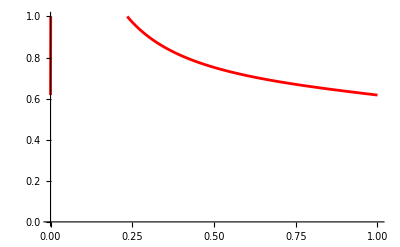

```mathematica
ListPlot[tt,Joined->True,PlotStyle->Hue[0],PlotRange->{{0,1},{0,1}}]
```

```mathematica
tt
```

{{0.,0.617284},{0.01,6.99428},{0.02,4.43882},{0.03,3.38625},{0.04,2.79569},{0.05,2.41344},{0.06,2.14428},{0.07,1.94385},{0.08,1.78848},{0.09,1.66435},{0.1,1.5628},{0.11,1.47812},{0.12,1.4064},{0.13,1.34484},{0.14,1.29141},{0.15,1.24458},{0.16,1.2032},{0.17,1.16635},{0.18,1.13332},{0.19,1.10355},{0.2,1.07656},{0.21,1.05199},{0.22,1.02952},{0.23,1.00888},{0.24,0.989857},{0.25,0.972269},{0.26,0.955955},{0.27,0.940779},{0.28,0.926624},{0.29,0.913389},{0.3,0.900984},{0.31,0.889332},{0.32,0.878365},{0.33,0.868022},{0.34,0.85825},{0.35,0.849002},{0.36,0.840235},{0.37,0.831911},{0.38,0.823995},{0.39,0.816458},{0.4,0.809271},{0.41,0.802409},{0.42,0.795849},{0.43,0.78957},{0.44,0.783554},{0.45,0.777783},{0.46,0.772242},{0.47,0.766914},{0.48,0.761788},{0.49,0.756851},{0.5,0.752091},{0.51,0.747498},{0.52,0.743062},{0.53,0.738774},{0.54,0.734626},{0.55,0.730609},{0.56,0.726717},{0.57,0.722943},{0.58,0.71928},{0.59,0.715722},{0.6,0.712263},{0.61,0.708899},{0.62,0.705625},{0.63,0.702436},{0.64,0.699327},{0.65,0.696295},{0.66,0.693335},{0.67,0.690444},{0.68,0.687618},{0.69,0.684854},{0.7,0.682149},{0.71,0.679501},{0.72,0.676905},{0.73,0.674359},{0.74,0.671862},{0.75,0.66941},{0.76,0.667},{0.77,0.664632},{0.78,0.662302},{0.79,0.660009},{0.8,0.65775},{0.81,0.655524},{0.82,0.653328},{0.83,0.651162},{0.84,0.649022},{0.85,0.646909},{0.86,0.644819},{0.87,0.642751},{0.88,0.640705},{0.89,0.638678},{0.9,0.636669},{0.91,0.634677},{0.92,0.6327},{0.93,0.630737},{0.94,0.628787},{0.95,0.626848},{0.96,0.624919},{0.97,0.623},{0.98,0.621088},{0.99,0.619183},{1.,0.617284}}